```mathematica
(*NEUE PUNKTE*)
(*60D rechts*)
a={710,999,1};
b={649,1082,1};
c={220,508,1};
d={424,880,1};
e={947,1191,1};
f={1383,310,1};
g={788,206,1};
h={1217,577,1};
i={848,1026,1};
j={236,571,1};
k={1213,765,1};
l={204,1107,1};
m={1439,599,1};


PC2={a,b,c,d,e,f,g,h,i,j,k,l,m};

(*6D links*)
aa={535,985,1};
bb={453,1077,1};
cc={134,431,1};
dd={363,854,1};
ee={799,1217,1};
ff={1589,132,1};
gg={784,47,1};
hh={1355,484,1};
ii={708,1023,1};
jj={147,504,1};
kk={1354,719,1};
ll={120,1108,1};
mm={1655,503,1};


PC1 ={aa,bb,cc,dd,ee,ff,gg,hh,ii,jj,kk,ll,mm};

PC1=PC1*(6.5)/1000;
PC1=Map[{#[[1]],#[[2]],1}&, PC1];
PC2=PC2*(4.29)/1000;
PC2=Map[{#[[1]],#[[2]],1}&, PC2];
```

```mathematica
ClearAll["Global`*"];
```

CemtroidPC1 = {4.998,4.542,1.}

CemtroidPC2 = {3.39174,3.24093,1.}

Mean[IntermediatePC1] = {2.73286×10^-16,-2.04964×10^-16}

Mean[IntermediatePC2] = {-1.02482×10^-16,-2.22045×10^-16}

MeanDistPC1 = 4.00996

MeanDistPC2 = 2.13565

(0.352675 | 0. | -1.76267
0. | 0.352675 | -1.60185
0. | 0. | 1.)

Matrix normalization PC1= {{-0.536243,0.656152},{-0.724219,0.867052},{-1.45549,-0.613831},{-0.930534,0.355849},{0.068948,1.18799},{1.87994,-1.29926},{0.0345622,-1.49411},{1.34352,-0.492335},{-0.139659,0.743263},{-1.42569,-0.446487},{1.34122,0.0463768},{-1.48758,0.938116},{2.03123,-0.448779}}

RMS distance=1.41421

(0.662193 | 0. | -2.24599
0. | 0.662193 | -2.14612
0. | 0. | 1.)

Matrix normalization PC2 = {{-0.229013,0.691846},{-0.402302,0.927633},{-1.62101,-0.702991},{-1.04148,0.35379},{0.444259,1.23728},{1.68285,-1.26547},{-0.00742981,-1.56092},{1.21128,-0.506975},{0.163019,0.768548},{-1.57556,-0.52402},{1.19991,0.0270969},{-1.66646,0.998653},{1.84194,-0.444477}}

RMS distance=1.41421

Begin Computation of Fundamentalmatrix________________________________________________

CoefficientMtx = (0.122806 | -0.150267 | -0.229013 | -0.370997 | 0.453956 | 0.691846 | -0.536243 | 0.656152 | 1.
0.291355 | -0.348817 | -0.402302 | -0.671809 | 0.804306 | 0.927633 | -0.724219 | 0.867052 | 1.
2.35936 | 0.995026 | -1.62101 | 1.0232 | 0.431518 | -0.702991 | -1.45549 | -0.613831 | 1.
0.969136 | -0.370611 | -1.04148 | -0.329213 | 0.125896 | 0.35379 | -0.930534 | 0.355849 | 1.
0.0306308 | 0.527773 | 0.444259 | 0.0853081 | 1.46987 | 1.23728 | 0.068948 | 1.18799 | 1.
3.16365 | -2.18645 | 1.68285 | -2.379 | 1.64417 | -1.26547 | 1.87994 | -1.29926 | 1.
-0.00025679 | 0.0111009 | -0.00742981 | -0.0539486 | 2.33218 | -1.56092 | 0.0345622 | -1.49411 | 1.
1.62737 | -0.596354 | 1.21128 | -0.681129 | 0.249601 | -0.506975 | 1.34352 | -0.492335 | 1.
-0.0227671 | 0.121166 | 0.163019 | -0.107335 | 0.571233 | 0.768548 | -0.139659 | 0.743263 | 1.
2.24625 | 0.703465 | -1.57556 | 0.74709 | 0.233968 | -0.52402 | -1.42569 | -0.446487 | 1.
1.60935 | 0.0556482 | 1.19991 | 0.0363431 | 0.00125667 | 0.0270969 | 1.34122 | 0.0463768 | 1.
2.479 | -1.56333 | -1.66646 | -1.48558 | 0.936853 | 0.998653 | -1.48758 | 0.938116 | 1.
3.7414 | -0.826623 | 1.84194 | -0.902837 | 0.199472 | -0.444477 | 2.03123 | -0.448779 | 1.)

Rank CoefficientMatx = 9

FFin = (0.00146235 | 0.0167371 | 0.0315719
-0.0431642 | 0.00244692 | -0.69285
-0.0294866 | 0.71811 | -0.0161027)

FFin Rank = 3

PC2NormTest = {{-0.229013,0.691846,1.},{-0.402302,0.927633,1.},{-1.62101,-0.702991,1.},{-1.04148,0.35379,1.},{0.444259,1.23728,1.},{1.68285,-1.26547,1.},{-0.00742981,-1.56092,1.},{1.21128,-0.506975,1.},{0.163019,0.768548,1.},{-1.57556,-0.52402,1.},{1.19991,0.0270969,1.},{-1.66646,0.998653,1.},{1.84194,-0.444477,1.}}

PC1NormTest = {{-0.536243,0.656152,1.},{-0.724219,0.867052,1.},{-1.45549,-0.613831,1.},{-0.930534,0.355849,1.},{0.068948,1.18799,1.},{1.87994,-1.29926,1.},{0.0345622,-1.49411,1.},{1.34352,-0.492335,1.},{-0.139659,0.743263,1.},{-1.42569,-0.446487,1.},{1.34122,0.0463768,1.},{-1.48758,0.938116,1.},{2.03123,-0.448779,1.}}

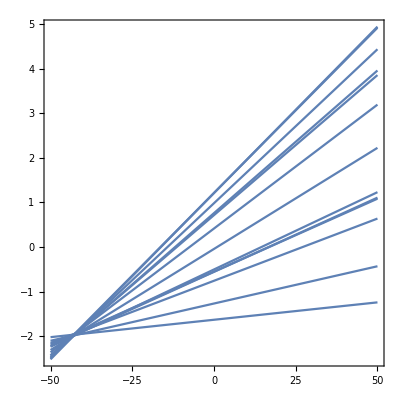

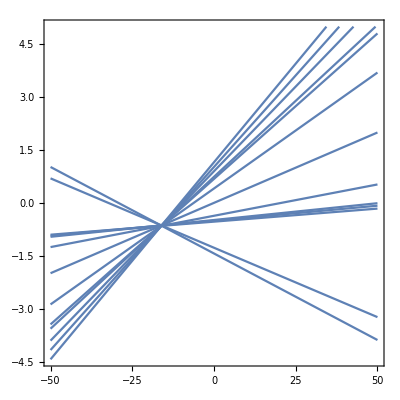

FPrime MatrixRank = 2

FPrime = (0.00129989 | 0.0167306 | 0.031582
-0.0431717 | 0.00244662 | -0.692849
-0.0294828 | 0.71811 | -0.0161029)

2

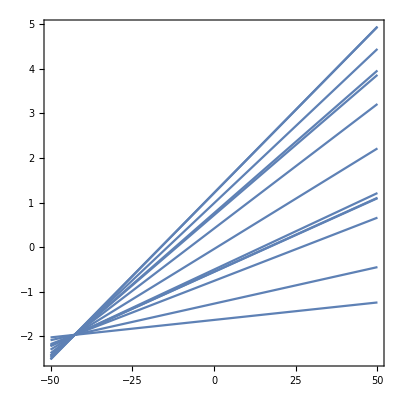

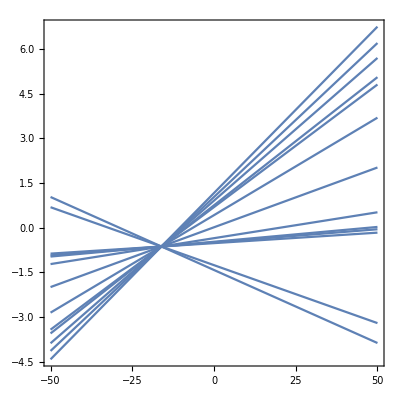

Demnormalized FPrime -> F =(0.000303575 | 0.00390726 | 0.00164931
-0.0100823 | 0.000571383 | -0.411004
0.0212484 | 0.238155 | 0.212001)

F Rank = 2

-0.000908311

-0.00201377

-0.0015204

-0.00156446

0.000533759

-0.000349109

-0.00059192

0.00240199

0.00244898

0.00161994

-0.00176362

0.000373447

-0.00163603

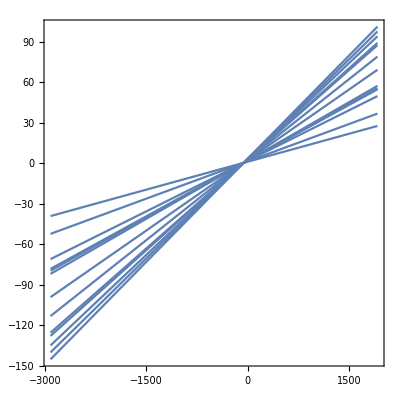

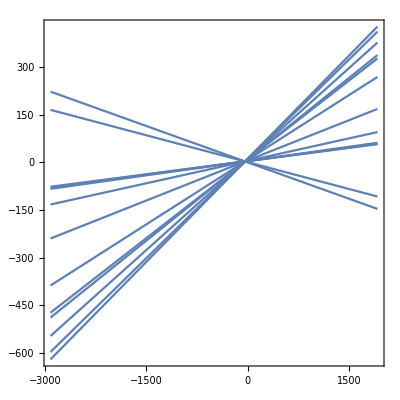

epipole ={-0.997442,0.0671286,0.0245614}

epipolePrime = {-0.999856,0.00444359,0.0163933}

Test F^T.e' = {0,0,0}

Test F.e = {0,0,0}

End Computation of Fundamentalmatrix________________________________________________

Begin Computation of Essential Matrix with K1 and K2___________________________________

PC1 = {{3.4775,6.4025,1},{2.9445,7.0005,1},{0.871,2.8015,1},{2.3595,5.551,1},{5.1935,7.9105,1},{10.3285,0.858,1},{5.096,0.3055,1},{8.8075,3.146,1},{4.602,6.6495,1},{0.9555,3.276,1},{8.801,4.6735,1},{0.78,7.202,1},{10.7575,3.2695,1}}

PC1mm = (3.4775 | 6.4025 | 1
2.9445 | 7.0005 | 1
0.871 | 2.8015 | 1
2.3595 | 5.551 | 1
5.1935 | 7.9105 | 1
10.3285 | 0.858 | 1
5.096 | 0.3055 | 1
8.8075 | 3.146 | 1
4.602 | 6.6495 | 1
0.9555 | 3.276 | 1
8.801 | 4.6735 | 1
0.78 | 7.202 | 1
10.7575 | 3.2695 | 1)

PC2mm = (3.0459 | 4.28571 | 1
2.78421 | 4.64178 | 1
0.9438 | 2.17932 | 1
1.81896 | 3.7752 | 1
4.06263 | 5.10939 | 1
5.93307 | 1.3299 | 1
3.38052 | 0.88374 | 1
5.22093 | 2.47533 | 1
3.63792 | 4.40154 | 1
1.01244 | 2.44959 | 1
5.20377 | 3.28185 | 1
0.87516 | 4.74903 | 1
6.17331 | 2.56971 | 1)

normalized Coordinates K1 = (-0.141203 | 0.129929 | 1.
-0.169968 | 0.162189 | 1.
-0.281867 | -0.0643308 | 1.
-0.201538 | 0.0839942 | 1.
-0.0485969 | 0.21128 | 1.
0.228521 | -0.169175 | 1.
-0.0538586 | -0.19898 | 1.
0.146438 | -0.0457463 | 1.
-0.0805181 | 0.143254 | 1.
-0.277307 | -0.0387333 | 1.
0.146087 | 0.0366564 | 1.
-0.286778 | 0.173059 | 1.
0.251673 | -0.039084 | 1.)

normalized Coordinates K2 = (-0.164495 | 0.0157366 | 1.
-0.178618 | 0.0349452 | 1.
-0.277938 | -0.097895 | 1.
-0.230709 | -0.0118034 | 1.
-0.109626 | 0.060171 | 1.
-0.00868484 | -0.143718 | 1.
-0.146437 | -0.167787 | 1.
-0.0471166 | -0.0819264 | 1.
-0.132546 | 0.0219852 | 1.
-0.274234 | -0.083315 | 1.
-0.0480426 | -0.0384178 | 1.
-0.281643 | 0.040731 | 1.
0.00428009 | -0.076835 | 1.)

EsMtx = {{0.104236,1.34211,0.354014},{-3.46317,0.196339,-8.71542},{-0.318163,4.89837,-0.468725}}

2

SVD of EMtx ={{{0.0297553,0.269536,0.962531},{-0.995299,-0.080804,0.0533957},{-0.0921684,0.959594,-0.265864}},{{9.41569,0.,0.},{0.,5.05845,0.},{0.,0.,0.}},{{0.369523,0.000519014,-0.929222},{-0.0644622,0.997605,-0.0250774},{0.926983,0.0691664,0.368671}}}

new SVD = {{{0.0297553,0.269536,0.962531},{-0.995299,-0.080804,0.0533957},{-0.0921684,0.959594,-0.265864}},{{7.23707,0.,0.},{0.,7.23707,0.},{0.,0.,0.}},{{0.369523,0.000519014,-0.929222},{-0.0644622,0.997605,-0.0250774},{0.926983,0.0691664,0.368671}}}

EPrime = {{0.0805859,1.9321,0.334537},{-2.66199,-0.119059,-6.71755},{-0.242878,6.97101,-0.137988}}

2

0.607554

0.701025

0.0133097

0.458687

0.867725

-0.323076

-0.404974

0.0772276

0.656676

0.0920483

0.335203

0.712822

0.096887

End Computation of Essential Matrix with K1 and K2___________________________________

Begin Computation of extern Cameraparameters with K1 and K2___________________________________

Begin Reconstruction of Rotation and Translation________________________________________________

E = (0.0805859 | 1.9321 | 0.334537
-2.66199 | -0.119059 | -6.71755
-0.242878 | 6.97101 | -0.137988)

U of E = {{0.271173,0.,0.962531},{-0.189528,-0.980422,0.0533957},{0.943686,-0.196906,-0.265864}}

Sigma of E = {{7.23707,0.,0.},{0.,7.23707,0.},{0.,0.,0.}}

V of E = {{0.0410629,0.367235,-0.929222},{0.984508,-0.173538,-0.0250774},{0.170465,0.913796,0.368671}}

ETest1 = {{0.0805859,1.9321,0.334537},{-2.66199,-0.119059,-6.71755},{-0.242878,6.97101,-0.137988}}

ETest2 = {{-0.0805859,-1.9321,-0.334537},{2.66199,0.119059,6.71755},{0.242878,-6.97101,0.137988}}

S1 = (0. | 0.265864 | 0.0533957
-0.265864 | 0. | -0.962531
-0.0533957 | 0.962531 | 0.)

S2 = (0. | -0.265864 | -0.0533957
0.265864 | 0. | 0.962531
0.0533957 | -0.962531 | 0.)

R1 = (0.993988 | -0.0229212 | -0.10706
0.0202741 | 0.999463 | -0.0257482
0.107593 | 0.0234229 | 0.993919)

R2 = (0.79482 | 0.0711967 | -0.602654
0.0789588 | -0.996785 | -0.0136227
-0.601687 | -0.0367573 | -0.797886)

1.

1.

Det E =1.43656×10^-15

Det F =-1.08469×10^-20

Check if t of S1, S2 is equal = {{{-0.962531,-0.0533957,0.265864}},{{0.962531,0.0533957,-0.265864}}}

R1 is Rotation = {{1.,0,0},{0,1.,0},{0,0,1.}}

R2 is Rotation ={{1.,0,0},{0,1.,0},{0,0,1.}}

Determinant of R1 = 1.

Determinant of R2 = 1.

Left E und S = {{0.962531,0.0533957,-0.265864}} , {{-0.962531,-0.0533957,0.265864}}

P1 = (0.993988 | -0.0229212 | -0.10706 | 0.962531
0.0202741 | 0.999463 | -0.0257482 | 0.0533957
0.107593 | 0.0234229 | 0.993919 | -0.265864)

P2 = (0.993988 | -0.0229212 | -0.10706 | -0.962531
0.0202741 | 0.999463 | -0.0257482 | -0.0533957
0.107593 | 0.0234229 | 0.993919 | 0.265864)

P3 = (0.79482 | 0.0711967 | -0.602654 | 0.962531
0.0789588 | -0.996785 | -0.0136227 | 0.0533957
-0.601687 | -0.0367573 | -0.797886 | -0.265864)

P4 = (0.79482 | 0.0711967 | -0.602654 | -0.962531
0.0789588 | -0.996785 | -0.0136227 | -0.0533957
-0.601687 | -0.0367573 | -0.797886 | 0.265864)

{-2.90557,0.110337,2.92724}

(-0.0111352 | -0.266972 | -0.0462255
0.367827 | 0.0164513 | 0.928214
0.0335603 | -0.963237 | 0.0190669)

End Reconstruction of Rotation and Translation________________________________________________

PC1mm = (3.4775 | 6.4025 | 1
2.9445 | 7.0005 | 1
0.871 | 2.8015 | 1
2.3595 | 5.551 | 1
5.1935 | 7.9105 | 1
10.3285 | 0.858 | 1
5.096 | 0.3055 | 1
8.8075 | 3.146 | 1
4.602 | 6.6495 | 1
0.9555 | 3.276 | 1
8.801 | 4.6735 | 1
0.78 | 7.202 | 1
10.7575 | 3.2695 | 1)

PC2mm= (3.0459 | 4.28571 | 1
2.78421 | 4.64178 | 1
0.9438 | 2.17932 | 1
1.81896 | 3.7752 | 1
4.06263 | 5.10939 | 1
5.93307 | 1.3299 | 1
3.38052 | 0.88374 | 1
5.22093 | 2.47533 | 1
3.63792 | 4.40154 | 1
1.01244 | 2.44959 | 1
5.20377 | 3.28185 | 1
0.87516 | 4.74903 | 1
6.17331 | 2.56971 | 1)

F = {{0.000303575,0.00390726,0.00164931},{-0.0100823,0.000571383,-0.411004},{0.0212484,0.238155,0.212001}}

T = (1 | 0 | -3.4775
0 | 1 | -6.4025
0 | 0 | 1)

TPrime = (1 | 0 | -3.0459
0 | 1 | -4.28571
0 | 0 | 1)

StructureF = (0.000303575 | 0.00390726 | 0.0277212
-0.0100823 | 0.000571383 | -0.442407
-0.0210366 | 0.252505 | -0.000908311)

epipole = (-0.9963
-0.0829219
0.0225982)

epipolePrime = (0.997919
0.0625616
-0.0155833)

epipole[[1]]^2+epipole[[2]]^2 = 0.999489

epipolePrime[[1]]^2+epipolePrime[[2]]^2 = 0.999757

epipole[[1]]^2+epipole[[2]]^2 = 1.

epipolePrime[[1]]^2+epipolePrime[[2]]^2 = 1.

R = {{0.996554,0.082943,0},{-0.082943,0.996554,0},{0,0,1}}

RPrime = {{0.998041,0.0625692,0},{-0.0625692,0.998041,0},{0,0,1}}

R is Rotation = {{1.,0.,0.},{0.,1.,0.},{0.,0.,1.}}

RPrime is Rotation = {{1.,0.,0.},{0.,1.,0.},{0.,0.,1.}}

R and epipole should be (1,0,e_3) = {1.,0.,0.0226039}

RPrime and epipolePrime should be (1,0,e_3') = {1.,0.,0.0155852}

RotatedF = (-3.19987×10^-7 | 0.00394899 | -0.0000141562
-0.0100198 | 0.00116086 | -0.443275
-0.0000205314 | 0.25338 | -0.000908311)

roots = {{root→-21.6982-64.2034 ⅈ},{root→-21.6982+64.2034 ⅈ},{root→0.000882827},{root→24.5547-50.5531 ⅈ},{root→24.5547+50.5531 ⅈ},{root→409.423}}

rootsReals = {{root→0.000882827},{root→409.423}}

root at Infinity = 5746.65

rootsReals = 2

st = {3.16475×10^-6,6049.91}

rootMin = 3.16475×10^-6

l = {7.15359×10^-8,1,-3.16475×10^-6}

lPrime = {0.0000141437,-0.443275,-0.000907509}

closestPointX = {3.4775,6.4025,1.}

closestPointXPrime= {3.04603,4.28367,1.}

K1Ex= (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0)

K2Ex= (0.993988 | -0.0229212 | -0.10706 | -0.962531
0.0202741 | 0.999463 | -0.0257482 | -0.0533957
0.107593 | 0.0234229 | 0.993919 | 0.265864)

P= (18.53 | 0. | 6.094 | 0.
0. | 18.537 | 3.994 | 0.
0. | 0. | 1. | 0.)

PPrime= (19.0743 | -0.28199 | 4.07312 | -16.2155
0.805547 | 18.6206 | 3.49242 | 0.0720655
0.107593 | 0.0234229 | 0.993919 | 0.265864)

Rank TestMtx = 4

TestMtx = (-18.53 | 0. | -2.6165 | 0.
0. | -18.537 | 2.4085 | 0.
-18.7465 | 0.353337 | -1.04561 | 17.0253
-0.344655 | -18.5203 | 0.7652 | 1.06681)

SVDTest = {{{0.553946,-0.0183586,0.832183,0.0166972},{-0.000399848,0.709667,0.0300452,-0.703896},{0.831962,-0.0139792,-0.553341,-0.0381853},{0.0313617,0.70416,-0.0195689,0.709079}},{{29.6021,0.,0.,0.},{0.,26.3104,0.,0.},{0.,0.,10.8203,0.},{0.,0.,0.,1.1767}},{{-0.873987,0.0136659,-0.465825,0.13772},{-0.00944028,-0.995851,-0.0360473,-0.0830176},{-0.0775714,0.0878249,-0.142458,-0.98284},{0.479625,0.0195057,-0.87259,0.0903658}}}

SpacePointPx ={1.52403,-0.918684,-10.8762,1.}

PC1mm = (3.4775 | 6.4025 | 1
2.9445 | 7.0005 | 1
0.871 | 2.8015 | 1
2.3595 | 5.551 | 1
5.1935 | 7.9105 | 1
10.3285 | 0.858 | 1
5.096 | 0.3055 | 1
8.8075 | 3.146 | 1
4.602 | 6.6495 | 1
0.9555 | 3.276 | 1
8.801 | 4.6735 | 1
0.78 | 7.202 | 1
10.7575 | 3.2695 | 1)

PC2mm= (3.0459 | 4.28571 | 1
2.78421 | 4.64178 | 1
0.9438 | 2.17932 | 1
1.81896 | 3.7752 | 1
4.06263 | 5.10939 | 1
5.93307 | 1.3299 | 1
3.38052 | 0.88374 | 1
5.22093 | 2.47533 | 1
3.63792 | 4.40154 | 1
1.01244 | 2.44959 | 1
5.20377 | 3.28185 | 1
0.87516 | 4.74903 | 1
6.17331 | 2.56971 | 1)

F = {{0.000303575,0.00390726,0.00164931},{-0.0100823,0.000571383,-0.411004},{0.0212484,0.238155,0.212001}}

T = (1 | 0 | -2.9445
0 | 1 | -7.0005
0 | 0 | 1)

TPrime = (1 | 0 | -2.78421
0 | 1 | -4.64178
0 | 0 | 1)

StructureF = (0.000303575 | 0.00390726 | 0.029896
-0.0100823 | 0.000571383 | -0.436691
-0.024706 | 0.251686 | -0.00201377)

epipole = (-0.994975
-0.0974859
0.0228443)

epipolePrime = (0.997538
0.0683637
-0.0156413)

epipole[[1]]^2+epipole[[2]]^2 = 0.999478

epipolePrime[[1]]^2+epipolePrime[[2]]^2 = 0.999755

epipole[[1]]^2+epipole[[2]]^2 = 1.

epipolePrime[[1]]^2+epipolePrime[[2]]^2 = 1.

R = {{0.995234,0.0975113,0},{-0.0975113,0.995234,0},{0,0,1}}

RPrime = {{0.99766,0.0683721,0},{-0.0683721,0.99766,0},{0,0,1}}

R is Rotation = {{1.,0.,0.},{0.,1.,0.},{0.,0.,1.}}

RPrime is Rotation = {{1.,0.,0.},{0.,1.,0.},{0.,0.,1.}}

R and epipole should be (1,0,e_3) = {1.,0.,0.0228502}

RPrime and epipolePrime should be (1,0,e_3') = {1.,0.,0.0156432}

RotatedF = (-7.19824×10^-7 | 0.00395611 | -0.0000315018
-0.0100019 | 0.00128431 | -0.437714
-0.0000460151 | 0.252896 | -0.00201377)

roots = {{root→-21.0192-64.0714 ⅈ},{root→-21.0192+64.0714 ⅈ},{root→0.00199285},{root→24.1356-49.2568 ⅈ},{root→24.1356+49.2568 ⅈ},{root→365.124}}

rootsReals = {{root→0.00199285},{root→365.124}}

root at Infinity = 5612.07

rootsReals = 2

st = {0.0000158689,5972.65}

rootMin = 0.0000158689

l = {3.62608×10^-7,1,-0.0000158689}

lPrime = {0.000031439,-0.437714,-0.00200975}

closestPointX = {2.9445,7.00052,1.}

closestPointXPrime= {2.78452,4.6372,1.}

K1Ex= (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0)

K2Ex= (0.993988 | -0.0229212 | -0.10706 | -0.962531
0.0202741 | 0.999463 | -0.0257482 | -0.0533957
0.107593 | 0.0234229 | 0.993919 | 0.265864)

P= (18.53 | 0. | 6.094 | 0.
0. | 18.537 | 3.994 | 0.
0. | 0. | 1. | 0.)

PPrime= (19.0743 | -0.28199 | 4.07312 | -16.2155
0.805547 | 18.6206 | 3.49242 | 0.0720655
0.107593 | 0.0234229 | 0.993919 | 0.265864)

Rank TestMtx = 4

TestMtx = (-18.53 | 0. | -3.1495 | 0.
0. | -18.537 | 3.00652 | 0.
-18.7747 | 0.347212 | -1.30552 | 16.9558
-0.306618 | -18.512 | 1.11658 | 1.1608)

SVDTest = {{{0.556789,-0.0139578,0.830364,0.0169353},{-0.012037,0.710832,0.0343456,-0.70242},{0.830281,0.0012215,-0.555893,-0.0401729},{0.0217763,0.703223,-0.0172703,0.710426}},{{29.6392,0.,0.,0.},{0.,26.3748,0.,0.},{0.,0.,10.8254,0.},{0.,0.,0.,1.35354}},{{-0.874257,0.000761469,-0.45676,0.164454},{0.00365361,-0.993155,-0.0471084,-0.106819},{-0.0961375,0.112406,-0.166785,-0.974836},{0.475836,0.0317353,-0.872544,0.106017}}}

SpacePointPx ={1.5512,-1.00757,-9.1951,1.}

PC1mm = (3.4775 | 6.4025 | 1
2.9445 | 7.0005 | 1
0.871 | 2.8015 | 1
2.3595 | 5.551 | 1
5.1935 | 7.9105 | 1
10.3285 | 0.858 | 1
5.096 | 0.3055 | 1
8.8075 | 3.146 | 1
4.602 | 6.6495 | 1
0.9555 | 3.276 | 1
8.801 | 4.6735 | 1
0.78 | 7.202 | 1
10.7575 | 3.2695 | 1)

PC2mm= (3.0459 | 4.28571 | 1
2.78421 | 4.64178 | 1
0.9438 | 2.17932 | 1
1.81896 | 3.7752 | 1
4.06263 | 5.10939 | 1
5.93307 | 1.3299 | 1
3.38052 | 0.88374 | 1
5.22093 | 2.47533 | 1
3.63792 | 4.40154 | 1
1.01244 | 2.44959 | 1
5.20377 | 3.28185 | 1
0.87516 | 4.74903 | 1
6.17331 | 2.56971 | 1)

F = {{0.000303575,0.00390726,0.00164931},{-0.0100823,0.000571383,-0.411004},{0.0212484,0.238155,0.212001}}

T = (1 | 0 | -0.871
0 | 1 | -2.8015
0 | 0 | 1)

TPrime = (1 | 0 | -0.9438
0 | 1 | -2.17932
0 | 0 | 1)

StructureF = (0.000303575 | 0.00390726 | 0.0128599
-0.0100823 | 0.000571383 | -0.418185
-0.000437535 | 0.243088 | -0.0015204)

epipole = (-0.999708
-0.00164864
0.0241003)

epipolePrime = (0.999396
0.0307918
-0.0161361)

epipole[[1]]^2+epipole[[2]]^2 = 0.999419

epipolePrime[[1]]^2+epipolePrime[[2]]^2 = 0.99974

epipole[[1]]^2+epipole[[2]]^2 = 1.

epipolePrime[[1]]^2+epipolePrime[[2]]^2 = 1.

R = {{0.999999,0.00164912,0},{-0.00164912,0.999999,0},{0,0,1}}

RPrime = {{0.999526,0.0307958,0},{-0.0307958,0.999526,0},{0,0,1}}

R is Rotation = {{1.,0.,0.},{0.,1.,0.},{0.,0.,1.}}

RPrime is Rotation = {{1.,0.,0.},{0.,1.,0.},{0.,0.,1.}}

R and epipole should be (1,0,e_3) = {1.,0.,0.0241073}

RPrime and epipolePrime should be (1,0,e_3') = {1.,0.,0.0161382}

RotatedF = (-5.91508×10^-7 | 0.00392301 | -0.0000245365
-0.0100861 | 0.000467418 | -0.418383
-0.0000366527 | 0.243089 | -0.0015204)

roots = {{root→-21.5837-55.7263 ⅈ},{root→-21.5837+55.7263 ⅈ},{root→0.00157853},{root→22.5649-50.6741 ⅈ},{root→22.5649+50.6741 ⅈ},{root→955.555}}

rootsReals = {{root→0.00157853},{root→955.555}}

root at Infinity = 5506.59

rootsReals = 2

st = {9.87295×10^-6,5556.88}

rootMin = 9.87295×10^-6

l = {2.3801×10^-7,1,-9.87295×10^-6}

lPrime = {0.0000244977,-0.418383,-0.001518}

closestPointX = {0.871,2.80151,1.}

closestPointXPrime= {0.943912,2.17569,1.}

K1Ex= (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0)

K2Ex= (0.993988 | -0.0229212 | -0.10706 | -0.962531
0.0202741 | 0.999463 | -0.0257482 | -0.0533957
0.107593 | 0.0234229 | 0.993919 | 0.265864)

P= (18.53 | 0. | 6.094 | 0.
0. | 18.537 | 3.994 | 0.
0. | 0. | 1. | 0.)

PPrime= (19.0743 | -0.28199 | 4.07312 | -16.2155
0.805547 | 18.6206 | 3.49242 | 0.0720655
0.107593 | 0.0234229 | 0.993919 | 0.265864)

Rank TestMtx = 4

TestMtx = (-18.53 | 0. | -5.223 | 0.
0. | -18.537 | -1.19249 | 0.
-18.9727 | 0.304099 | -3.13494 | 16.4665
-0.571458 | -18.5696 | -1.32995 | 0.506374)

SVDTest = {{{0.570574,-0.0410996,0.820217,-0.000171755},{0.0511439,0.704571,-0.000421056,-0.707788},{0.816097,-0.0811768,-0.571781,-0.0214974},{0.0762516,0.703776,-0.0176307,0.706098}},{{29.9968,0.,0.,0.},{0.,26.2739,0.,0.},{0.,0.,10.6662,0.},{0.,0.,0.,0.0280823}},{{-0.87009,0.0722976,-0.406923,0.268572},{-0.0705357,-0.995443,0.0151246,0.0623681},{-0.190051,-0.0497465,-0.231343,-0.952831},{0.449276,-0.0373116,-0.883553,0.126858}}}

SpacePointPx ={2.11711,0.491638,-7.51101,1.}

PC1mm = (3.4775 | 6.4025 | 1
2.9445 | 7.0005 | 1
0.871 | 2.8015 | 1
2.3595 | 5.551 | 1
5.1935 | 7.9105 | 1
10.3285 | 0.858 | 1
5.096 | 0.3055 | 1
8.8075 | 3.146 | 1
4.602 | 6.6495 | 1
0.9555 | 3.276 | 1
8.801 | 4.6735 | 1
0.78 | 7.202 | 1
10.7575 | 3.2695 | 1)

PC2mm= (3.0459 | 4.28571 | 1
2.78421 | 4.64178 | 1
0.9438 | 2.17932 | 1
1.81896 | 3.7752 | 1
4.06263 | 5.10939 | 1
5.93307 | 1.3299 | 1
3.38052 | 0.88374 | 1
5.22093 | 2.47533 | 1
3.63792 | 4.40154 | 1
1.01244 | 2.44959 | 1
5.20377 | 3.28185 | 1
0.87516 | 4.74903 | 1
6.17331 | 2.56971 | 1)

F = {{0.000303575,0.00390726,0.00164931},{-0.0100823,0.000571383,-0.411004},{0.0212484,0.238155,0.212001}}

T = (1 | 0 | -2.3595
0 | 1 | -5.551
0 | 0 | 1)

TPrime = (1 | 0 | -1.81896
0 | 1 | -3.7752
0 | 0 | 1)

StructureF = (0.000303575 | 0.00390726 | 0.0240548
-0.0100823 | 0.000571383 | -0.431622
-0.016262 | 0.24742 | -0.00156446)

epipole = (-0.997588
-0.0654208
0.0232161)

epipolePrime = (0.998321
0.0556953
-0.0158941)

epipole[[1]]^2+epipole[[2]]^2 = 0.999461

epipolePrime[[1]]^2+epipolePrime[[2]]^2 = 0.999747

epipole[[1]]^2+epipole[[2]]^2 = 1.

epipolePrime[[1]]^2+epipolePrime[[2]]^2 = 1.

R = {{0.997857,0.0654385,0},{-0.0654385,0.997857,0},{0,0,1}}

RPrime = {{0.998447,0.0557023,0},{-0.0557023,0.998447,0},{0,0,1}}

R is Rotation = {{1.,0.,0.},{0.,1.,0.},{0.,0.,1.}}

RPrime is Rotation = {{1.,0.,0.},{0.,1.,0.},{0.,0.,1.}}

R and epipole should be (1,0,e_3) = {1.,0.,0.0232224}

RPrime and epipolePrime should be (1,0,e_3') = {1.,0.,0.0158961}

RotatedF = (-5.77513×10^-7 | 0.00394151 | -0.0000248688
-0.0100388 | 0.00101195 | -0.432291
-0.0000363304 | 0.247954 | -0.00156446)

roots = {{root→-21.4653-61.4565 ⅈ},{root→-21.4653+61.4565 ⅈ},{root→0.00156191},{root→23.8303-49.9261 ⅈ},{root→23.8303+49.9261 ⅈ},{root→457.522}}

rootsReals = {{root→0.00156191},{root→457.522}}

root at Infinity = 5567.06

rootsReals = 2

st = {9.85492×10^-6,5794.36}

rootMin = 9.85492×10^-6

l = {2.28855×10^-7,1,-9.85492×10^-6}

lPrime = {0.00002483,-0.432291,-0.00156201}

closestPointX = {2.3595,5.55101,1.}

closestPointXPrime= {1.81916,3.77159,1.}

K1Ex= (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0)

K2Ex= (0.993988 | -0.0229212 | -0.10706 | -0.962531
0.0202741 | 0.999463 | -0.0257482 | -0.0533957
0.107593 | 0.0234229 | 0.993919 | 0.265864)

P= (18.53 | 0. | 6.094 | 0.
0. | 18.537 | 3.994 | 0.
0. | 0. | 1. | 0.)

PPrime= (19.0743 | -0.28199 | 4.07312 | -16.2155
0.805547 | 18.6206 | 3.49242 | 0.0720655
0.107593 | 0.0234229 | 0.993919 | 0.265864)

Rank TestMtx = 4

TestMtx = (-18.53 | 0. | -3.7345 | 0.
0. | -18.537 | 1.55701 | 0.
-18.8785 | 0.3246 | -2.26502 | 16.6992
-0.399751 | -18.5323 | 0.256239 | 0.930666)

SVDTest = {{{0.561925,-0.0157692,0.826971,0.0105273},{-0.000526784,0.708145,0.0228448,-0.705697},{0.826584,-0.015818,-0.561523,-0.0346675},{0.031612,0.705714,-0.0170309,0.707586}},{{29.7439,0.,0.,0.},{0.,26.2514,0.,0.},{0.,0.,10.6648,0.},{0.,0.,0.,0.90038}},{{-0.875132,0.0117599,-0.442222,0.196075},{-0.0103473,-0.99844,-0.0272037,-0.0476539},{-0.133253,0.0524976,-0.167397,-0.975431},{0.46506,0.0149568,-0.880726,0.0884174}}}

SpacePointPx ={2.21761,-0.538965,-11.0321,1.}

PC1mm = (3.4775 | 6.4025 | 1
2.9445 | 7.0005 | 1
0.871 | 2.8015 | 1
2.3595 | 5.551 | 1
5.1935 | 7.9105 | 1
10.3285 | 0.858 | 1
5.096 | 0.3055 | 1
8.8075 | 3.146 | 1
4.602 | 6.6495 | 1
0.9555 | 3.276 | 1
8.801 | 4.6735 | 1
0.78 | 7.202 | 1
10.7575 | 3.2695 | 1)

PC2mm= (3.0459 | 4.28571 | 1
2.78421 | 4.64178 | 1
0.9438 | 2.17932 | 1
1.81896 | 3.7752 | 1
4.06263 | 5.10939 | 1
5.93307 | 1.3299 | 1
3.38052 | 0.88374 | 1
5.22093 | 2.47533 | 1
3.63792 | 4.40154 | 1
1.01244 | 2.44959 | 1
5.20377 | 3.28185 | 1
0.87516 | 4.74903 | 1
6.17331 | 2.56971 | 1)

F = {{0.000303575,0.00390726,0.00164931},{-0.0100823,0.000571383,-0.411004},{0.0212484,0.238155,0.212001}}

T = (1 | 0 | -5.1935
0 | 1 | -7.9105
0 | 0 | 1)

TPrime = (1 | 0 | -4.06263
0 | 1 | -5.10939
0 | 0 | 1)

StructureF = (0.000303575 | 0.00390726 | 0.0341343
-0.0100823 | 0.000571383 | -0.458846
-0.0290325 | 0.256949 | 0.000533759)

epipole = (-0.993438
-0.112293
0.0216891)

epipolePrime = (0.997129
0.0741601
-0.0153276)

epipole[[1]]^2+epipole[[2]]^2 = 0.99953

epipolePrime[[1]]^2+epipolePrime[[2]]^2 = 0.999765

epipole[[1]]^2+epipole[[2]]^2 = 1.

epipolePrime[[1]]^2+epipolePrime[[2]]^2 = 1.

R = {{0.993672,0.11232,0},{-0.11232,0.993672,0},{0,0,1}}

RPrime = {{0.997246,0.0741688,0},{-0.0741688,0.997246,0},{0,0,1}}

R is Rotation = {{1.,0.,0.},{0.,1.,0.},{0.,0.,1.}}

RPrime is Rotation = {{1.,0.,0.},{0.,1.,0.},{0.,0.,1.}}

R and epipole should be (1,0,e_3) = {1.,0.,0.0216942}

RPrime and epipolePrime should be (1,0,e_3') = {1.,0.,0.0153294}

RotatedF = (1.77506×10^-7 | 0.00396394 | 8.18222×10^-6
-0.0099818 | 0.00141009 | -0.460114
0.0000115795 | 0.258584 | 0.000533759)

roots = {{root→-21.9778-69.116 ⅈ},{root→-21.9778+69.116 ⅈ},{root→-0.000495463},{root→25.8496-51.521 ⅈ},{root→25.8496+51.521 ⅈ},{root→351.165}}

rootsReals = {{root→-0.000495463},{root→351.165}}

root at Infinity = 5902.24

rootsReals = 2

st = {1.02271×10^-6,6341.56}

rootMin = 1.02271×10^-6

l = {2.21869×10^-8,1,-1.02271×10^-6}

lPrime = {-8.18627×10^-6,-0.460114,0.000534023}

closestPointX = {5.1935,7.9105,1.}

closestPointXPrime= {4.06254,5.11055,1.}

K1Ex= (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0)

K2Ex= (0.993988 | -0.0229212 | -0.10706 | -0.962531
0.0202741 | 0.999463 | -0.0257482 | -0.0533957
0.107593 | 0.0234229 | 0.993919 | 0.265864)

P= (18.53 | 0. | 6.094 | 0.
0. | 18.537 | 3.994 | 0.
0. | 0. | 1. | 0.)

PPrime= (19.0743 | -0.28199 | 4.07312 | -16.2155
0.805547 | 18.6206 | 3.49242 | 0.0720655
0.107593 | 0.0234229 | 0.993919 | 0.265864)

Rank TestMtx = 4

TestMtx = (-18.53 | 0. | -0.9005 | 0.
0. | -18.537 | 3.9165 | 0.
-18.6372 | 0.377147 | -0.0352768 | 17.2956
-0.255689 | -18.5009 | 1.58705 | 1.28665)

SVDTest = {{{0.546195,-0.0307162,0.836356,0.0351481},{0.0155324,0.713442,0.0454368,-0.699067},{0.836279,-0.0312104,-0.545244,-0.0487101},{0.0454657,0.699345,-0.033952,0.712529}},{{29.5492,0.,0.,0.},{0.,26.4894,0.,0.},{0.,0.,10.8942,0.},{0.,0.,0.,1.65816}},{{-0.870362,0.036695,-0.488993,0.0448317},{-0.0275365,-0.988143,-0.0385303,-0.146053},{-0.0131429,0.148469,-0.0559778,-0.987244},{0.491466,0.0135906,-0.869637,0.0448105}}}

SpacePointPx ={1.00047,-3.25934,-22.0315,1.}

PC1mm = (3.4775 | 6.4025 | 1
2.9445 | 7.0005 | 1
0.871 | 2.8015 | 1
2.3595 | 5.551 | 1
5.1935 | 7.9105 | 1
10.3285 | 0.858 | 1
5.096 | 0.3055 | 1
8.8075 | 3.146 | 1
4.602 | 6.6495 | 1
0.9555 | 3.276 | 1
8.801 | 4.6735 | 1
0.78 | 7.202 | 1
10.7575 | 3.2695 | 1)

PC2mm= (3.0459 | 4.28571 | 1
2.78421 | 4.64178 | 1
0.9438 | 2.17932 | 1
1.81896 | 3.7752 | 1
4.06263 | 5.10939 | 1
5.93307 | 1.3299 | 1
3.38052 | 0.88374 | 1
5.22093 | 2.47533 | 1
3.63792 | 4.40154 | 1
1.01244 | 2.44959 | 1
5.20377 | 3.28185 | 1
0.87516 | 4.74903 | 1
6.17331 | 2.56971 | 1)

F = {{0.000303575,0.00390726,0.00164931},{-0.0100823,0.000571383,-0.411004},{0.0212484,0.238155,0.212001}}

T = (1 | 0 | -10.3285
0 | 1 | -0.858
0 | 0 | 1)

TPrime = (1 | 0 | -5.93307
0 | 1 | -1.3299
0 | 0 | 1)

StructureF = (0.000303575 | 0.00390726 | 0.00813721
-0.0100823 | 0.000571383 | -0.514649
0.00964116 | 0.262097 | -0.000349109)

epipole = (-0.999131
0.0367788
0.0196144)

epipolePrime = (-0.999763
-0.0158176
0.0149386)

epipole[[1]]^2+epipole[[2]]^2 = 0.999615

epipolePrime[[1]]^2+epipolePrime[[2]]^2 = 0.999777

epipole[[1]]^2+epipole[[2]]^2 = 1.

epipolePrime[[1]]^2+epipolePrime[[2]]^2 = 1.

R = {{0.999323,0.0367859,0},{-0.0367859,0.999323,0},{0,0,1}}

RPrime = {{0.999875,0.0158194,0},{-0.0158194,0.999875,0},{0,0,1}}

R is Rotation = {{1.,0.,0.},{0.,1.,0.},{0.,0.,1.}}

RPrime is Rotation = {{1.,0.,0.},{0.,1.,0.},{0.,0.,1.}}

R and epipole should be (1,0,e_3) = {1.,0.,0.0196182}

RPrime and epipolePrime should be (1,0,e_3') = {1.,0.,0.0149403}

RotatedF = (0.000287991 | 0.00390786 | -5.21579×10^-6
-0.0100602 | 0.000880172 | -0.514713
0.0192761 | 0.261565 | -0.000349109)

roots = {{root→-27.4838-75.0148 ⅈ},{root→-27.4838+75.0148 ⅈ},{root→0.000273934},{root→30.435-61.8059 ⅈ},{root→30.435+61.8059 ⅈ},{root→634.966}}

rootsReals = {{root→0.000273934},{root→634.966}}

root at Infinity = 6862.01

rootsReals = 2

st = {3.65618×10^-7,7060.25}

rootMin = 3.65618×10^-7

l = {7.17276×10^-9,1,-3.65618×10^-7}

lPrime = {5.21436×10^-6,-0.514713,-0.000349014}

closestPointX = {10.3285,0.858,1.}

closestPointXPrime= {5.93308,1.32922,1.}

K1Ex= (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0)

K2Ex= (0.993988 | -0.0229212 | -0.10706 | -0.962531
0.0202741 | 0.999463 | -0.0257482 | -0.0533957
0.107593 | 0.0234229 | 0.993919 | 0.265864)

P= (18.53 | 0. | 6.094 | 0.
0. | 18.537 | 3.994 | 0.
0. | 0. | 1. | 0.)

PPrime= (19.0743 | -0.28199 | 4.07312 | -16.2155
0.805547 | 18.6206 | 3.49242 | 0.0720655
0.107593 | 0.0234229 | 0.993919 | 0.265864)

Rank TestMtx = 4

TestMtx = (-18.53 | 0. | 4.2345 | 0.
0. | -18.537 | -3.136 | 0.
-18.4359 | 0.42096 | 1.82389 | 17.7929
-0.662533 | -18.5895 | -2.17128 | 0.281327)

SVDTest = {{{0.550359,-0.0215366,0.834265,-0.0253616},{-0.046965,-0.706848,-0.00871958,-0.705751},{0.833389,-0.0417159,-0.551067,-0.00686967},{-0.0190155,-0.705806,0.0158464,0.707972}},{{29.8549,0.,0.,0.},{0.,26.5167,0.,0.},{0.,0.,11.4339,0.},{0.,0.,0.,0.581409}},{{-0.855802,0.061688,-0.464406,0.219372},{0.052752,0.988276,-0.0319154,-0.139677},{0.13529,0.135081,0.220445,0.95648},{0.496504,-0.0354798,-0.857154,0.132334}}}

SpacePointPx ={1.65771,-1.05548,7.22775,1.}

PC1mm = (3.4775 | 6.4025 | 1
2.9445 | 7.0005 | 1
0.871 | 2.8015 | 1
2.3595 | 5.551 | 1
5.1935 | 7.9105 | 1
10.3285 | 0.858 | 1
5.096 | 0.3055 | 1
8.8075 | 3.146 | 1
4.602 | 6.6495 | 1
0.9555 | 3.276 | 1
8.801 | 4.6735 | 1
0.78 | 7.202 | 1
10.7575 | 3.2695 | 1)

PC2mm= (3.0459 | 4.28571 | 1
2.78421 | 4.64178 | 1
0.9438 | 2.17932 | 1
1.81896 | 3.7752 | 1
4.06263 | 5.10939 | 1
5.93307 | 1.3299 | 1
3.38052 | 0.88374 | 1
5.22093 | 2.47533 | 1
3.63792 | 4.40154 | 1
1.01244 | 2.44959 | 1
5.20377 | 3.28185 | 1
0.87516 | 4.74903 | 1
6.17331 | 2.56971 | 1)

F = {{0.000303575,0.00390726,0.00164931},{-0.0100823,0.000571383,-0.411004},{0.0212484,0.238155,0.212001}}

T = (1 | 0 | -5.096
0 | 1 | -0.3055
0 | 0 | 1)

TPrime = (1 | 0 | -3.38052
0 | 1 | -0.88374
0 | 0 | 1)

StructureF = (0.000303575 | 0.00390726 | 0.00438999
-0.0100823 | 0.000571383 | -0.462209
0.0133646 | 0.251869 | -0.00059192)

epipole = (-0.998354
0.0530256
0.0218429)

epipolePrime = (-0.999834
-0.00951617
0.0155321)

epipole[[1]]^2+epipole[[2]]^2 = 0.999523

epipolePrime[[1]]^2+epipolePrime[[2]]^2 = 0.999759

epipole[[1]]^2+epipole[[2]]^2 = 1.

epipolePrime[[1]]^2+epipolePrime[[2]]^2 = 1.

R = {{0.998592,0.0530383,0},{-0.0530383,0.998592,0},{0,0,1}}

RPrime = {{0.999955,0.00951732,0},{-0.00951732,0.999955,0},{0,0,1}}

R is Rotation = {{1.,0.,0.},{0.,1.,0.},{0.,0.,1.}}

RPrime is Rotation = {{1.,0.,0.},{0.,1.,0.},{0.,0.,1.}}

R and epipole should be (1,0,e_3) = {1.,0.,0.0218481}

RPrime and epipolePrime should be (1,0,e_3') = {1.,0.,0.015534}

RotatedF = (0.000414826 | 0.003896 | -9.19485×10^-6
-0.0100422 | 0.00106829 | -0.46223
0.0267045 | 0.250806 | -0.00059192)

roots = {{root→-23.6305-67.0128 ⅈ},{root→-23.6305+67.0128 ⅈ},{root→0.000536798},{root→26.4713-53.4608 ⅈ},{root→26.4713+53.4608 ⅈ},{root→464.634}}

rootsReals = {{root→0.000536798},{root→464.634}}

root at Infinity = 5949.3

rootsReals = 2

st = {1.26689×10^-6,6217.49}

rootMin = 1.26689×10^-6

l = {2.7679×10^-8,1,-1.26689×10^-6}

lPrime = {9.18991×10^-6,-0.46223,-0.000591602}

closestPointX = {5.096,0.305501,1.}

closestPointXPrime= {3.38053,0.88246,1.}

K1Ex= (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0)

K2Ex= (0.993988 | -0.0229212 | -0.10706 | -0.962531
0.0202741 | 0.999463 | -0.0257482 | -0.0533957
0.107593 | 0.0234229 | 0.993919 | 0.265864)

P= (18.53 | 0. | 6.094 | 0.
0. | 18.537 | 3.994 | 0.
0. | 0. | 1. | 0.)

PPrime= (19.0743 | -0.28199 | 4.07312 | -16.2155
0.805547 | 18.6206 | 3.49242 | 0.0720655
0.107593 | 0.0234229 | 0.993919 | 0.265864)

Rank TestMtx = 4

TestMtx = (-18.53 | 0. | -0.998 | 0.
0. | -18.537 | -3.6885 | 0.
-18.7106 | 0.361172 | -0.713141 | 17.1143
-0.710601 | -18.5999 | -2.61532 | 0.162549)

SVDTest = {{{0.548967,-0.0271903,0.835216,0.0175994},{0.0397452,0.708111,-0.0179215,0.704754},{0.832614,-0.0679352,-0.549623,0.00732626},{0.0617206,0.702299,-0.00276025,-0.709196}},{{29.552,0.,0.,0.},{0.,26.627,0.,0.},{0.,0.,10.7519,0.},{0.,0.,0.,0.779495}},{{-0.872863,0.047917,-0.482784,0.0522891},{-0.0536017,-0.98447,0.0172102,0.166282},{-0.0490545,-0.164233,-0.0342511,-0.984606},{0.482525,-0.0393774,-0.8749,0.0129629}}}

SpacePointPx ={4.03376,12.8275,-75.9558,1.}

PC1mm = (3.4775 | 6.4025 | 1
2.9445 | 7.0005 | 1
0.871 | 2.8015 | 1
2.3595 | 5.551 | 1
5.1935 | 7.9105 | 1
10.3285 | 0.858 | 1
5.096 | 0.3055 | 1
8.8075 | 3.146 | 1
4.602 | 6.6495 | 1
0.9555 | 3.276 | 1
8.801 | 4.6735 | 1
0.78 | 7.202 | 1
10.7575 | 3.2695 | 1)

PC2mm= (3.0459 | 4.28571 | 1
2.78421 | 4.64178 | 1
0.9438 | 2.17932 | 1
1.81896 | 3.7752 | 1
4.06263 | 5.10939 | 1
5.93307 | 1.3299 | 1
3.38052 | 0.88374 | 1
5.22093 | 2.47533 | 1
3.63792 | 4.40154 | 1
1.01244 | 2.44959 | 1
5.20377 | 3.28185 | 1
0.87516 | 4.74903 | 1
6.17331 | 2.56971 | 1)

F = {{0.000303575,0.00390726,0.00164931},{-0.0100823,0.000571383,-0.411004},{0.0212484,0.238155,0.212001}}

T = (1 | 0 | -8.8075
0 | 1 | -3.146
0 | 0 | 1)

TPrime = (1 | 0 | -5.22093
0 | 1 | -2.47533
0 | 0 | 1)

StructureF = (0.000303575 | 0.00390726 | 0.0166153
-0.0100823 | 0.000571383 | -0.498006
-0.00212356 | 0.259969 | 0.00240199)

epipole = (-0.99976
-0.00835346
0.0202308)

epipolePrime = (0.999332
0.0332685
-0.0150928)

epipole[[1]]^2+epipole[[2]]^2 = 0.999591

epipolePrime[[1]]^2+epipolePrime[[2]]^2 = 0.999772

epipole[[1]]^2+epipole[[2]]^2 = 1.

epipolePrime[[1]]^2+epipolePrime[[2]]^2 = 1.

R = {{0.999965,0.00835517,0},{-0.00835517,0.999965,0},{0,0,1}}

RPrime = {{0.999446,0.0332723,0},{-0.0332723,0.999446,0},{0,0,1}}

R is Rotation = {{1.,0.,0.},{0.,1.,0.},{0.,0.,1.}}

RPrime is Rotation = {{1.,0.,0.},{0.,1.,0.},{0.,0.,1.}}

R and epipole should be (1,0,e_3) = {1.,0.,0.020235}

RPrime and epipolePrime should be (1,0,e_3') = {1.,0.,0.0150945}

RotatedF = (7.33656×10^-7 | 0.00392424 | 0.0000362568
-0.0100828 | 0.000525324 | -0.498283
0.0000486042 | 0.259978 | 0.00240199)

roots = {{root→-27.0286-69.3162 ⅈ},{root→-27.0286+69.3162 ⅈ},{root→-0.00197694},{root→28.645-61.8513 ⅈ},{root→28.645+61.8513 ⅈ},{root→1028.13}}

rootsReals = {{root→-0.00197694},{root→1028.13}}

root at Infinity = 6753.98

rootsReals = 2

st = {0.0000182652,6825.14}

rootMin = 0.0000182652

l = {3.69597×10^-7,1,-0.0000182652}

lPrime = {-0.0000363285,-0.498283,0.00240674}

closestPointX = {8.8075,3.14602,1.}

closestPointXPrime= {5.22077,2.48016,1.}

K1Ex= (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0)

K2Ex= (0.993988 | -0.0229212 | -0.10706 | -0.962531
0.0202741 | 0.999463 | -0.0257482 | -0.0533957
0.107593 | 0.0234229 | 0.993919 | 0.265864)

P= (18.53 | 0. | 6.094 | 0.
0. | 18.537 | 3.994 | 0.
0. | 0. | 1. | 0.)

PPrime= (19.0743 | -0.28199 | 4.07312 | -16.2155
0.805547 | 18.6206 | 3.49242 | 0.0720655
0.107593 | 0.0234229 | 0.993919 | 0.265864)

Rank TestMtx = 4

TestMtx = (-18.53 | 0. | 2.7135 | 0.
0. | -18.537 | -0.847982 | 0.
-18.5126 | 0.404276 | 1.11591 | 17.6035
-0.5387 | -18.5625 | -1.02734 | 0.58732)

SVDTest = {{{0.546906,-0.00854016,-0.837137,-0.00483247},{0.00165632,0.706305,-0.0102094,0.707832},{0.836767,-0.0183919,0.546712,0.0242797},{0.0266959,0.707617,0.0142969,-0.705947}},{{29.6741,0.,0.,0.},{0.,26.2715,0.,0.},{0.,0.,11.161,0.},{0.,0.,0.,0.141246}},{{-0.864029,0.00447392,0.482344,0.144149},{-0.00633424,-0.998624,0.0129817,-0.0504121},{0.0805064,-0.0521324,-0.149407,0.984113},{0.496923,0.00349563,0.863049,0.0905609}}}

SpacePointPx ={1.59173,-0.556665,10.8669,1.}

PC1mm = (3.4775 | 6.4025 | 1
2.9445 | 7.0005 | 1
0.871 | 2.8015 | 1
2.3595 | 5.551 | 1
5.1935 | 7.9105 | 1
10.3285 | 0.858 | 1
5.096 | 0.3055 | 1
8.8075 | 3.146 | 1
4.602 | 6.6495 | 1
0.9555 | 3.276 | 1
8.801 | 4.6735 | 1
0.78 | 7.202 | 1
10.7575 | 3.2695 | 1)

PC2mm= (3.0459 | 4.28571 | 1
2.78421 | 4.64178 | 1
0.9438 | 2.17932 | 1
1.81896 | 3.7752 | 1
4.06263 | 5.10939 | 1
5.93307 | 1.3299 | 1
3.38052 | 0.88374 | 1
5.22093 | 2.47533 | 1
3.63792 | 4.40154 | 1
1.01244 | 2.44959 | 1
5.20377 | 3.28185 | 1
0.87516 | 4.74903 | 1
6.17331 | 2.56971 | 1)

F = {{0.000303575,0.00390726,0.00164931},{-0.0100823,0.000571383,-0.411004},{0.0212484,0.238155,0.212001}}

T = (1 | 0 | -4.602
0 | 1 | -6.6495
0 | 0 | 1)

TPrime = (1 | 0 | -3.63792
0 | 1 | -4.40154
0 | 0 | 1)

StructureF = (0.000303575 | 0.00390726 | 0.0290277
-0.0100823 | 0.000571383 | -0.453603
-0.0220247 | 0.254885 | 0.00244898)

epipole = (-0.996027
-0.0862788
0.0220301)

epipolePrime = (0.997845
0.0637723
-0.0154394)

epipole[[1]]^2+epipole[[2]]^2 = 0.999515

epipolePrime[[1]]^2+epipolePrime[[2]]^2 = 0.999762

epipole[[1]]^2+epipole[[2]]^2 = 1.

epipolePrime[[1]]^2+epipolePrime[[2]]^2 = 1.

R = {{0.996269,0.0862997,0},{-0.0862997,0.996269,0},{0,0,1}}

RPrime = {{0.997964,0.0637799,0},{-0.0637799,0.997964,0},{0,0,1}}

R is Rotation = {{1.,0.,0.},{0.,1.,0.},{0.,0.,1.}}

RPrime is Rotation = {{1.,0.,0.},{0.,1.,0.},{0.,0.,1.}}

R and epipole should be (1,0,e_3) = {1.,0.,0.0220354}

RPrime and epipolePrime should be (1,0,e_3') = {1.,0.,0.0154413}

RotatedF = (8.33279×10^-7 | 0.00395041 | 0.0000378154
-0.0100158 | 0.00118981 | -0.454531
0.0000539644 | 0.255835 | 0.00244898)

roots = {{root→-22.3261-66.4437 ⅈ},{root→-22.3261+66.4437 ⅈ},{root→-0.00230302},{root→25.4264-51.8894 ⅈ},{root→25.4264+51.8894 ⅈ},{root→410.527}}

rootsReals = {{root→-0.00230302},{root→410.527}}

root at Infinity = 5904.71

rootsReals = 2

st = {0.0000220454,6226.83}

rootMin = 0.0000220454

l = {4.8578×10^-7,1,-0.0000220454}

lPrime = {-0.0000379025,-0.454531,0.00245462}

closestPointX = {4.602,6.64952,1.}

closestPointXPrime= {3.63758,4.40693,1.}

K1Ex= (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0)

K2Ex= (0.993988 | -0.0229212 | -0.10706 | -0.962531
0.0202741 | 0.999463 | -0.0257482 | -0.0533957
0.107593 | 0.0234229 | 0.993919 | 0.265864)

P= (18.53 | 0. | 6.094 | 0.
0. | 18.537 | 3.994 | 0.
0. | 0. | 1. | 0.)

PPrime= (19.0743 | -0.28199 | 4.07312 | -16.2155
0.805547 | 18.6206 | 3.49242 | 0.0720655
0.107593 | 0.0234229 | 0.993919 | 0.265864)

Rank TestMtx = 4

TestMtx = (-18.53 | 0. | -1.492 | 0.
0. | -18.537 | 2.65552 | 0.
-18.6829 | 0.367193 | -0.457661 | 17.1826
-0.331393 | -18.5174 | 0.887713 | 1.09958)

SVDTest = {{{0.548934,-0.0233299,0.83521,0.0234756},{0.00882705,0.710201,0.0337997,-0.703131},{0.834908,-0.0250357,-0.548277,-0.041162},{0.0390237,0.703166,-0.025948,0.709479}},{{29.5542,0.,0.,0.},{0.,26.3301,0.,0.},{0.,0.,10.8429,0.},{0.,0.,0.,1.26515}},{{-0.872402,0.0253329,-0.481831,0.078177},{-0.0196138,-0.994868,-0.0320376,-0.0939527},{-0.0386758,0.0970915,-0.0856312,-0.99083},{0.486861,0.0130272,-0.871481,0.0575891}}}

SpacePointPx ={1.3575,-1.63143,-17.2052,1.}

PC1mm = (3.4775 | 6.4025 | 1
2.9445 | 7.0005 | 1
0.871 | 2.8015 | 1
2.3595 | 5.551 | 1
5.1935 | 7.9105 | 1
10.3285 | 0.858 | 1
5.096 | 0.3055 | 1
8.8075 | 3.146 | 1
4.602 | 6.6495 | 1
0.9555 | 3.276 | 1
8.801 | 4.6735 | 1
0.78 | 7.202 | 1
10.7575 | 3.2695 | 1)

PC2mm= (3.0459 | 4.28571 | 1
2.78421 | 4.64178 | 1
0.9438 | 2.17932 | 1
1.81896 | 3.7752 | 1
4.06263 | 5.10939 | 1
5.93307 | 1.3299 | 1
3.38052 | 0.88374 | 1
5.22093 | 2.47533 | 1
3.63792 | 4.40154 | 1
1.01244 | 2.44959 | 1
5.20377 | 3.28185 | 1
0.87516 | 4.74903 | 1
6.17331 | 2.56971 | 1)

F = {{0.000303575,0.00390726,0.00164931},{-0.0100823,0.000571383,-0.411004},{0.0212484,0.238155,0.212001}}

T = (1 | 0 | -0.9555
0 | 1 | -3.276
0 | 0 | 1)

TPrime = (1 | 0 | -1.01244
0 | 1 | -2.44959
0 | 0 | 1)

StructureF = (0.000303575 | 0.00390726 | 0.0147396
-0.0100823 | 0.000571383 | -0.418766
-0.00314163 | 0.243511 | 0.00161994)

epipole = (-0.999626
-0.0130566
0.0240493)

epipolePrime = (0.999254
0.035109
-0.0161159)

epipole[[1]]^2+epipole[[2]]^2 = 0.999422

epipolePrime[[1]]^2+epipolePrime[[2]]^2 = 0.99974

epipole[[1]]^2+epipole[[2]]^2 = 1.

epipolePrime[[1]]^2+epipolePrime[[2]]^2 = 1.

R = {{0.999915,0.0130603,0},{-0.0130603,0.999915,0},{0,0,1}}

RPrime = {{0.999383,0.0351136,0},{-0.0351136,0.999383,0},{0,0,1}}

R is Rotation = {{1.,0.,0.},{0.,1.,0.},{0.,0.,1.}}

RPrime is Rotation = {{1.,0.,0.},{0.,1.,0.},{0.,0.,1.}}

R and epipole should be (1,0,e_3) = {1.,0.,0.0240563}

RPrime and epipolePrime should be (1,0,e_3') = {1.,0.,0.016118}

RotatedF = (6.28115×10^-7 | 0.00392524 | 0.0000261102
-0.0100802 | 0.000565531 | -0.419025
0.0000389697 | 0.243531 | 0.00161994)

roots = {{root→-21.4724-56.3971 ⅈ},{root→-21.4724+56.3971 ⅈ},{root→-0.00167954},{root→22.6615-50.2785 ⅈ},{root→22.6615+50.2785 ⅈ},{root→791.109}}

rootsReals = {{root→-0.00167954},{root→791.109}}

root at Infinity = 5498.98

rootsReals = 2

st = {0.000011172,5572.18}

rootMin = 0.000011172

l = {2.68758×10^-7,1,-0.000011172}

lPrime = {-0.0000261541,-0.419025,0.00162266}

closestPointX = {0.9555,3.27601,1.}

closestPointXPrime= {1.0123,2.45346,1.}

K1Ex= (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0)

K2Ex= (0.993988 | -0.0229212 | -0.10706 | -0.962531
0.0202741 | 0.999463 | -0.0257482 | -0.0533957
0.107593 | 0.0234229 | 0.993919 | 0.265864)

P= (18.53 | 0. | 6.094 | 0.
0. | 18.537 | 3.994 | 0.
0. | 0. | 1. | 0.)

PPrime= (19.0743 | -0.28199 | 4.07312 | -16.2155
0.805547 | 18.6206 | 3.49242 | 0.0720655
0.107593 | 0.0234229 | 0.993919 | 0.265864)

Rank TestMtx = 4

TestMtx = (-18.53 | 0. | -5.1385 | 0.
0. | -18.537 | -0.717989 | 0.
-18.9654 | 0.305701 | -3.06697 | 16.4846
-0.541573 | -18.5631 | -1.05388 | 0.580222)

SVDTest = {{{0.570325,-0.0355818,0.820647,0.000900689},{0.040341,0.705242,0.00331909,-0.70781},{0.817693,-0.0676737,-0.57118,-0.0235029},{0.066937,0.704832,-0.0167338,0.706011}},{{29.9714,0.,0.,0.},{0.,26.2477,0.,0.},{0.,0.,10.6723,0.},{0.,0.,0.,0.176323}},{{-0.871236,0.0594745,-0.408993,0.26483},{-0.0580683,-0.99733,0.00698029,0.0437238},{-0.184775,-0.032718,-0.229552,-0.955036},{0.451036,-0.0269211,-0.883166,0.125936}}}

SpacePointPx ={2.10289,0.34719,-7.58349,1.}

PC1mm = (3.4775 | 6.4025 | 1
2.9445 | 7.0005 | 1
0.871 | 2.8015 | 1
2.3595 | 5.551 | 1
5.1935 | 7.9105 | 1
10.3285 | 0.858 | 1
5.096 | 0.3055 | 1
8.8075 | 3.146 | 1
4.602 | 6.6495 | 1
0.9555 | 3.276 | 1
8.801 | 4.6735 | 1
0.78 | 7.202 | 1
10.7575 | 3.2695 | 1)

PC2mm= (3.0459 | 4.28571 | 1
2.78421 | 4.64178 | 1
0.9438 | 2.17932 | 1
1.81896 | 3.7752 | 1
4.06263 | 5.10939 | 1
5.93307 | 1.3299 | 1
3.38052 | 0.88374 | 1
5.22093 | 2.47533 | 1
3.63792 | 4.40154 | 1
1.01244 | 2.44959 | 1
5.20377 | 3.28185 | 1
0.87516 | 4.74903 | 1
6.17331 | 2.56971 | 1)

F = {{0.000303575,0.00390726,0.00164931},{-0.0100823,0.000571383,-0.411004},{0.0212484,0.238155,0.212001}}

T = (1 | 0 | -8.801
0 | 1 | -4.6735
0 | 0 | 1)

TPrime = (1 | 0 | -5.20377
0 | 1 | -3.28185
0 | 0 | 1)

StructureF = (0.000303575 | 0.00390726 | 0.0225817
-0.0100823 | 0.000571383 | -0.497068
-0.0102603 | 0.260363 | -0.00176362)

epipole = (-0.999026
-0.0392324
0.0202186)

epipolePrime = (0.998854
0.0454312
-0.0150895)

epipole[[1]]^2+epipole[[2]]^2 = 0.999591

epipolePrime[[1]]^2+epipolePrime[[2]]^2 = 0.999772

epipole[[1]]^2+epipole[[2]]^2 = 1.

epipolePrime[[1]]^2+epipolePrime[[2]]^2 = 1.

R = {{0.99923,0.0392404,0},{-0.0392404,0.99923,0},{0,0,1}}

RPrime = {{0.998967,0.0454363,0},{-0.0454363,0.998967,0},{0,0,1}}

R is Rotation = {{1.,0.,0.},{0.,1.,0.},{0.,0.,1.}}

RPrime is Rotation = {{1.,0.,0.},{0.,1.,0.},{0.,0.,1.}}

R and epipole should be (1,0,e_3) = {1.,0.,0.0202228}

RPrime and epipolePrime should be (1,0,e_3') = {1.,0.,0.0150912}

RotatedF = (-5.38231×10^-7 | 0.00393224 | -0.0000266151
-0.0100625 | 0.000788723 | -0.497581
-0.0000356653 | 0.260565 | -0.00176362)

roots = {{root→-26.318-71.2831 ⅈ},{root→-26.318+71.2831 ⅈ},{root→0.00145662},{root→28.7887-60.0777 ⅈ},{root→28.7887+60.0777 ⅈ},{root→683.988}}

rootsReals = {{root→0.00145662},{root→683.988}}

root at Infinity = 6666.31

rootsReals = 2

st = {9.85913×10^-6,6822.35}

rootMin = 9.85913×10^-6

l = {1.99379×10^-7,1,-9.85913×10^-6}

lPrime = {0.0000265763,-0.497581,-0.00176105}

closestPointX = {8.801,4.67351,1.}

closestPointXPrime= {5.20393,3.27831,1.}

K1Ex= (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0)

K2Ex= (0.993988 | -0.0229212 | -0.10706 | -0.962531
0.0202741 | 0.999463 | -0.0257482 | -0.0533957
0.107593 | 0.0234229 | 0.993919 | 0.265864)

P= (18.53 | 0. | 6.094 | 0.
0. | 18.537 | 3.994 | 0.
0. | 0. | 1. | 0.)

PPrime= (19.0743 | -0.28199 | 4.07312 | -16.2155
0.805547 | 18.6206 | 3.49242 | 0.0720655
0.107593 | 0.0234229 | 0.993919 | 0.265864)

Rank TestMtx = 4

TestMtx = (-18.53 | 0. | 2.707 | 0.
0. | -18.537 | 0.67951 | 0.
-18.5144 | 0.403881 | 1.09917 | 17.5991
-0.452824 | -18.5438 | -0.234039 | 0.799521)

SVDTest = {{{0.546578,-0.0200634,-0.836851,-0.0230158},{0.0188786,0.706766,-0.0240529,0.706787},{0.836092,-0.039122,0.546048,0.0353711},{0.0429598,0.70608,0.0305521,-0.706167}},{{29.6767,0.,0.,0.},{0.,26.2232,0.,0.},{0.,0.,11.1652,0.},{0.,0.,0.,0.631496}},{{-0.86355,0.029606,0.482148,0.144702},{-0.0272574,-0.999516,0.0089435,0.0120344},{0.0809177,0.00830144,-0.151242,0.985144},{0.496982,-0.00472802,0.86289,0.091692}}}

SpacePointPx ={1.57813,0.131249,10.7441,1.}

PC1mm = (3.4775 | 6.4025 | 1
2.9445 | 7.0005 | 1
0.871 | 2.8015 | 1
2.3595 | 5.551 | 1
5.1935 | 7.9105 | 1
10.3285 | 0.858 | 1
5.096 | 0.3055 | 1
8.8075 | 3.146 | 1
4.602 | 6.6495 | 1
0.9555 | 3.276 | 1
8.801 | 4.6735 | 1
0.78 | 7.202 | 1
10.7575 | 3.2695 | 1)

PC2mm= (3.0459 | 4.28571 | 1
2.78421 | 4.64178 | 1
0.9438 | 2.17932 | 1
1.81896 | 3.7752 | 1
4.06263 | 5.10939 | 1
5.93307 | 1.3299 | 1
3.38052 | 0.88374 | 1
5.22093 | 2.47533 | 1
3.63792 | 4.40154 | 1
1.01244 | 2.44959 | 1
5.20377 | 3.28185 | 1
0.87516 | 4.74903 | 1
6.17331 | 2.56971 | 1)

F = {{0.000303575,0.00390726,0.00164931},{-0.0100823,0.000571383,-0.411004},{0.0212484,0.238155,0.212001}}

T = (1 | 0 | -0.78
0 | 1 | -7.202
0 | 0 | 1)

TPrime = (1 | 0 | -0.87516
0 | 1 | -4.74903
0 | 0 | 1)

StructureF = (0.000303575 | 0.00390726 | 0.0300262
-0.0100823 | 0.000571383 | -0.414753
-0.0263669 | 0.244288 | 0.000373447)

epipole = (-0.993935
-0.107315
0.0240138)

epipolePrime = (0.997261
0.0721825
-0.0161195)

epipole[[1]]^2+epipole[[2]]^2 = 0.999423

epipolePrime[[1]]^2+epipolePrime[[2]]^2 = 0.99974

epipole[[1]]^2+epipole[[2]]^2 = 1.

epipolePrime[[1]]^2+epipolePrime[[2]]^2 = 1.

R = {{0.994222,0.107346,0},{-0.107346,0.994222,0},{0,0,1}}

RPrime = {{0.997391,0.0721919,0},{-0.0721919,0.997391,0},{0,0,1}}

R is Rotation = {{1.,0.,0.},{0.,1.,0.},{0.,0.,1.}}

RPrime is Rotation = {{1.,0.,0.},{0.,1.,0.},{0.,0.,1.}}

R and epipole should be (1,0,e_3) = {1.,0.,0.0240207}

RPrime and epipolePrime should be (1,0,e_3') = {1.,0.,0.0161216}

RotatedF = (1.44618×10^-7 | 0.00396119 | 6.02055×10^-6
-0.00998875 | 0.00136798 | -0.415839
8.97047×10^-6 | 0.245707 | 0.000373447)

roots = {{root→-19.5798-60.9493 ⅈ},{root→-19.5798+60.9493 ⅈ},{root→-0.000393318},{root→22.6352-46.2383 ⅈ},{root→22.6352+46.2383 ⅈ},{root→324.844}}

rootsReals = {{root→-0.000393318},{root→324.844}}

root at Infinity = 5170.69

rootsReals = 2

st = {5.97797×10^-7,5550.78}

rootMin = 5.97797×10^-7

l = {1.43595×10^-8,1,-5.97797×10^-7}

lPrime = {-6.02292×10^-6,-0.415839,0.000373594}

closestPointX = {0.78,7.202,1.}

closestPointXPrime= {0.875095,4.74993,1.}

K1Ex= (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0)

K2Ex= (0.993988 | -0.0229212 | -0.10706 | -0.962531
0.0202741 | 0.999463 | -0.0257482 | -0.0533957
0.107593 | 0.0234229 | 0.993919 | 0.265864)

P= (18.53 | 0. | 6.094 | 0.
0. | 18.537 | 3.994 | 0.
0. | 0. | 1. | 0.)

PPrime= (19.0743 | -0.28199 | 4.07312 | -16.2155
0.805547 | 18.6206 | 3.49242 | 0.0720655
0.107593 | 0.0234229 | 0.993919 | 0.265864)

Rank TestMtx = 4

TestMtx = (-18.53 | 0. | -5.314 | 0.
0. | -18.537 | 3.208 | 0.
-18.9801 | 0.302487 | -3.20334 | 16.4482
-0.294489 | -18.5093 | 1.22862 | 1.19077)

SVDTest = {{{0.572705,-0.00691446,-0.819666,0.0104333},{-0.0460343,-0.709705,-0.0351146,-0.702116},{0.81844,-0.0409537,0.571673,-0.0408556},{-0.00683555,-0.703273,0.0102043,0.710813}},{{29.9986,0.,0.,0.},{0.,26.3957,0.,0.},{0.,0.,10.6638,0.},{0.,0.,0.,1.3757}},{{-0.871516,0.0421484,0.406513,0.270981},{0.0409161,0.991091,0.059544,-0.111887},{-0.194048,-0.112627,0.227342,-0.947616},{0.448477,-0.0572461,0.882903,0.126783}}}

SpacePointPx ={2.13736,-0.882508,-7.4743,1.}

PC1mm = (3.4775 | 6.4025 | 1
2.9445 | 7.0005 | 1
0.871 | 2.8015 | 1
2.3595 | 5.551 | 1
5.1935 | 7.9105 | 1
10.3285 | 0.858 | 1
5.096 | 0.3055 | 1
8.8075 | 3.146 | 1
4.602 | 6.6495 | 1
0.9555 | 3.276 | 1
8.801 | 4.6735 | 1
0.78 | 7.202 | 1
10.7575 | 3.2695 | 1)

PC2mm= (3.0459 | 4.28571 | 1
2.78421 | 4.64178 | 1
0.9438 | 2.17932 | 1
1.81896 | 3.7752 | 1
4.06263 | 5.10939 | 1
5.93307 | 1.3299 | 1
3.38052 | 0.88374 | 1
5.22093 | 2.47533 | 1
3.63792 | 4.40154 | 1
1.01244 | 2.44959 | 1
5.20377 | 3.28185 | 1
0.87516 | 4.74903 | 1
6.17331 | 2.56971 | 1)

F = {{0.000303575,0.00390726,0.00164931},{-0.0100823,0.000571383,-0.411004},{0.0212484,0.238155,0.212001}}

T = (1 | 0 | -10.7575
0 | 1 | -3.2695
0 | 0 | 1)

TPrime = (1 | 0 | -6.17331
0 | 1 | -2.56971
0 | 0 | 1)

StructureF = (0.000303575 | 0.00390726 | 0.0176898
-0.0100823 | 0.000571383 | -0.517596
-0.00278601 | 0.263745 | -0.00163603)

epipole = (-0.999756
-0.01044
0.0194628)

epipolePrime = (0.999304
0.0342001
-0.0148783)

epipole[[1]]^2+epipole[[2]]^2 = 0.999621

epipolePrime[[1]]^2+epipolePrime[[2]]^2 = 0.999779

epipole[[1]]^2+epipole[[2]]^2 = 1.

epipolePrime[[1]]^2+epipolePrime[[2]]^2 = 1.

R = {{0.999945,0.0104419,0},{-0.0104419,0.999945,0},{0,0,1}}

RPrime = {{0.999415,0.0342039,0},{-0.0342039,0.999415,0},{0,0,1}}

R is Rotation = {{1.,0.,0.},{0.,1.,0.},{0.,0.,1.}}

RPrime is Rotation = {{1.,0.,0.},{0.,1.,0.},{0.,0.,1.}}

R and epipole should be (1,0,e_3) = {1.,0.,0.0194664}

RPrime and epipolePrime should be (1,0,e_3') = {1.,0.,0.01488}

RotatedF = (-4.73894×10^-7 | 0.00392474 | -0.0000243441
-0.0100816 | 0.000542706 | -0.517898
-0.0000318477 | 0.263759 | -0.00163603)

roots = {{root→-28.3641-72.8258 ⅈ},{root→-28.3641+72.8258 ⅈ},{root→0.00127748},{root→30.194-64.6194 ⅈ},{root→30.194+64.6194 ⅈ},{root→1038.4}}

rootsReals = {{root→0.00127748},{root→1038.4}}

root at Infinity = 7070.61

rootsReals = 2

st = {7.92392×10^-6,7148.33}

rootMin = 7.92392×10^-6

l = {1.54251×10^-7,1,-7.92392×10^-6}

lPrime = {0.000024313,-0.517898,-0.00163394}

closestPointX = {10.7575,3.26951,1.}

closestPointXPrime= {6.17342,2.56656,1.}

K1Ex= (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0)

K2Ex= (0.993988 | -0.0229212 | -0.10706 | -0.962531
0.0202741 | 0.999463 | -0.0257482 | -0.0533957
0.107593 | 0.0234229 | 0.993919 | 0.265864)

P= (18.53 | 0. | 6.094 | 0.
0. | 18.537 | 3.994 | 0.
0. | 0. | 1. | 0.)

PPrime= (19.0743 | -0.28199 | 4.07312 | -16.2155
0.805547 | 18.6206 | 3.49242 | 0.0720655
0.107593 | 0.0234229 | 0.993919 | 0.265864)

Rank TestMtx = 4

TestMtx = (-18.53 | 0. | 4.6635 | 0.
0. | -18.537 | -0.724492 | 0.
-18.4101 | 0.426589 | 2.06276 | 17.8568
-0.529404 | -18.5605 | -0.941468 | 0.61029)

SVDTest = {{{0.552122,-0.00340807,-0.833723,-0.00747641},{-0.00651352,0.706245,-0.0135477,0.707808},{0.833549,-0.00728965,0.551808,0.025506},{0.0177394,0.707922,0.0151841,-0.705905}},{{29.9144,0.,0.,0.},{0.,26.2643,0.,0.},{0.,0.,11.524,0.},{0.,0.,0.,0.176725}},{{-0.855305,-0.00675525,0.45835,0.241502},{0.00491646,-0.998851,0.0177635,-0.044241},{0.14315,-0.0460353,-0.239005,0.959305},{0.497933,0.0114935,0.855848,0.139478}}}

SpacePointPx ={1.73147,-0.317189,6.87781,1.}

SpacePointsMMNotScaled= (1.52403 | -0.918684 | -10.8762 | 1.
1.5512 | -1.00757 | -9.1951 | 1.
2.11711 | 0.491638 | -7.51101 | 1.
2.21761 | -0.538965 | -11.0321 | 1.
1.00047 | -3.25934 | -22.0315 | 1.
1.65771 | -1.05548 | 7.22775 | 1.
4.03376 | 12.8275 | -75.9558 | 1.
1.59173 | -0.556665 | 10.8669 | 1.
1.3575 | -1.63143 | -17.2052 | 1.
2.10289 | 0.34719 | -7.58349 | 1.
1.57813 | 0.131249 | 10.7441 | 1.
2.13736 | -0.882508 | -7.4743 | 1.
1.73147 | -0.317189 | 6.87781 | 1.)

SpacePointsMMNotScaled= (1.52403 | -0.918684 | -10.8762 | 1.
1.5512 | -1.00757 | -9.1951 | 1.
2.11711 | 0.491638 | -7.51101 | 1.
2.21761 | -0.538965 | -11.0321 | 1.
1.00047 | -3.25934 | -22.0315 | 1.
1.65771 | -1.05548 | 7.22775 | 1.
4.03376 | 12.8275 | -75.9558 | 1.
1.59173 | -0.556665 | 10.8669 | 1.
1.3575 | -1.63143 | -17.2052 | 1.
2.10289 | 0.34719 | -7.58349 | 1.
1.57813 | 0.131249 | 10.7441 | 1.
2.13736 | -0.882508 | -7.4743 | 1.
1.73147 | -0.317189 | 6.87781 | 1.)

SpacePoints = ((1. WorldPointsStart⟦1,1⟧
-0.602799 WorldPointsStart⟦1,1⟧
-7.1365 WorldPointsStart⟦1,1⟧) | (1.01783 WorldPointsStart⟦1,1⟧
-0.66112 WorldPointsStart⟦1,1⟧
-6.03341 WorldPointsStart⟦1,1⟧) | (1.38915 WorldPointsStart⟦1,1⟧
0.322591 WorldPointsStart⟦1,1⟧
-4.92839 WorldPointsStart⟦1,1⟧) | (1.45509 WorldPointsStart⟦1,1⟧
-0.353645 WorldPointsStart⟦1,1⟧
-7.23878 WorldPointsStart⟦1,1⟧) | (0.656466 WorldPointsStart⟦1,1⟧
-2.13863 WorldPointsStart⟦1,1⟧
-14.4561 WorldPointsStart⟦1,1⟧) | (1.08771 WorldPointsStart⟦1,1⟧
-0.692561 WorldPointsStart⟦1,1⟧
4.74252 WorldPointsStart⟦1,1⟧) | (2.64677 WorldPointsStart⟦1,1⟧
8.41685 WorldPointsStart⟦1,1⟧
-49.8388 WorldPointsStart⟦1,1⟧) | (1.04442 WorldPointsStart⟦1,1⟧
-0.365258 WorldPointsStart⟦1,1⟧
7.13035 WorldPointsStart⟦1,1⟧) | (0.890728 WorldPointsStart⟦1,1⟧
-1.07047 WorldPointsStart⟦1,1⟧
-11.2893 WorldPointsStart⟦1,1⟧) | (1.37982 WorldPointsStart⟦1,1⟧
0.227811 WorldPointsStart⟦1,1⟧
-4.97595 WorldPointsStart⟦1,1⟧) | (1.03549 WorldPointsStart⟦1,1⟧
0.0861194 WorldPointsStart⟦1,1⟧
7.04976 WorldPointsStart⟦1,1⟧) | (1.40244 WorldPointsStart⟦1,1⟧
-0.579062 WorldPointsStart⟦1,1⟧
-4.9043 WorldPointsStart⟦1,1⟧) | (1.13611 WorldPointsStart⟦1,1⟧
-0.208125 WorldPointsStart⟦1,1⟧
4.51291 WorldPointsStart⟦1,1⟧))

```mathematica
NormalizeCoordinates[PC1,PC2];
```